# An overview of the Weaver package

The following provides documentation of the commands in the Weaver (W-algebra exact arithmetic Verma module evaluator) package for performing calculations in modules of W-algebras.

A W-algebra is an algebra that is generated by the modes of a finite number of simple fields and superfields whose (anti-)commutation relations close under the inclusion of normal-ordered products of fields and derivatives of fields and satisfy a Jacobi Identity.

This package works with Verma modules of highest weight vectors of fields.  It starts by defining highest weight vectors v_i, which are annihilated by the positive modes: X_n v_i= 0 when n > 0, and which transform under a representation of the 0-modes.

The Verma module is the representation generated by the action of the universal enveloping algebra of the W-algebra on the highest weight vector (i.e. by the action of creation operators).

Examples of use of the package are provided in attached Mathematica notebook, Weaver_examples.nb.  That notebook describes the construction of two algebras, the Virasoro algebra and the SW(3/2,2) algebra as well as a number of examples of use of the package to isolate the structure of minimal models for these two algebras.

This notebook will provide a comprehensive overview of the commands and capabilities of the Weaver package.

## Loading the package

To begin, verify that the file Weaver.m is in Mathematica’s path.  If it is not, Mathematica’s path may be modified by appending a directory to the $Path variable.

Once you have done so, you may load the package using the following command.  Loading the package clears any previously completed calculations performed by the package, so must be done each time the algebra is changed.

```mathematica
<<Weaver.m
```

Weaver: a package for explicit exact-arithmetic calculations in operator algebras

## Constructing Algebras and Representations

Algebras may be defined by providing a particular set of parameters.  OperatorList and HighestWeightDimension must be defined for the entire algebra.  Δ, FermionQ, HC, and Grading must be defined for each operator.  operator[0] must be defined for each operator with integer grading.  Commutator must be defined for each ordered pair of operators.

The additional variables MinimalGeneratorsCreation, and MinimalGeneratorsAnnihilation must be defined for the entire algebra in order to perform certain calculations.

The examples for the following operators will describe the creation of the N=1 super Virasoro algebra at c=12 in the NS sector acting on the vacuum Verma module.

#### OperatorList

OperatorList is a list of the names of the simple operators in the theory.  Each of these names without parameters should be unbound.

```mathematica
OperatorList= {L,G};
```

#### HighestWeightDimension

HighestWeightDimension should be set to the dimension of the highest-weight space.  The 0-modes of the algebra should form a HighestWeightDimension dimension of this space.

```mathematica
HighestWeightDimension=1;
```

#### Δ

Δ[operator] should be set to the conformal weight of the operator for each operator in OperatorList.

```mathematica
Δ[L]=2;Δ[G]=3/2;
```

#### FermionQ

For each operator in OperatorList, FermionQ needs to be set to True if the operator is a fermion and False otherwise.

```mathematica
FermionQ[L]=False;
FermionQ[G]=True;
```

#### HC

HC[X, n, level] gives the matrix form of the Hermitian conjugate of X_n acting on level (level+n) on the left or level on the right.  In general, HC[X, n, level] should be set to Operator[X, -n, level-n], although this may be changed if X has a nonstandard Hermetian conjugate.

```mathematica
HC[L,n,level]:=Operator[L,-n,level-n];
HC[G,n,level]:=Operator[G,-n,level-n];
```

#### Grading

For each operator, Grading should be set to 0 if the modes of the operator are integer graded and 1/2 if the modes of the operator are half-integer graded.

```mathematica
Grading[L]=0;
Grading[G]=1/2;
```

#### operator[0]

operator[0] should be defined for each operator with integer grading.  It should take matrix values that form a representation of the 0-mode algebra on the highest-weight space, or a scalar value if that dimension is 1.

```mathematica
L[0]=0;
```

#### AddOperator

AddOperator[operator, fermionq, grading, conformal_weight] initializes a new 
operator named operator by adding it to OperatorList, setting FermionQ[operator]=fermionq, Grading[operator]=grading, Δ[operator]=conformal_weight, and HC[operator,n,level]:=Operator[operator,-n,level-n].

```mathematica
Clear[OperatorList];
AddOperator[L,False,0,2];
AddOperator[G,True,1/2,3/2];
```

#### Commutator

Commutator[X, m, Y, n, level] gives an expression for the (anti-)commutator [X_m,Y_n] acting on level.  Commutator should be defined in terms of δ[n+m,level], Operator[Z, m+n, level], NOperator[Z, W, m+n, level], and NOperator[Z, a, W, b, m+n, level] which are expressions for Subscript[δ, n + m], Subscript[Z, n], :ZW:_(n+m), and :∂^a Z∂^b W:_(n+m), respectively.

```mathematica
Commutator[L,m_,L,n_,level_]:=(n-m)Operator[L,n+m,level]+(n^3-n)δ[m+n,level]
Commutator[G,m_,G,n_,level_]:=2Operator[L,n+m,level]+(4m^2-1)δ[m+n,level]
Commutator[L,m_,G,n_,level_]:=(m/2-n)Operator[G,n+m,level]
Commutator[G,n_,L,m_,level_]:=-Commutator[L,m,G,n,level]
```

#### MinimalGeneratorsCreation and MinimalGeneratorsAnnihilation

MinimalGeneratorsCreation (resp. MinimalGeneratorsAnnihilation) should be set to a list of operators that that generate the negative (resp positive) level space of operators.  They do not need to be minimal, but including redundant operators may slow certain calculations.  Operators should be listed as {X,n} to represent X_n.

```mathematica
MinimalGeneratorsAnnihilation={{L,1},{G,1/2},{G,3/2}};
MinimalGeneratorsCreation={{L,-1},{G,-1/2},{G,-3/2}};
```

## Functions describing operators

Included here is a list of commands provided by the package that describe the subspaces of the Verma modules and linear action of Operators.  Examples of their use are provided on the super Virasoro representation defined above.

#### FSign

FSign[X,Y] returns -1 if both X and Y are fermionic and 1 otherwise.

```mathematica
FSign[L,G]
FSign[G,G]
```

1

-1

#### OperatorNames

OperatorNames[level] returns a list of all of the operators in the universal covering algebra of the negative subalgebra at a given level.  Each operator is given as a product of operators in OperatorList, listing those operators by {operator_name,level}.

```mathematica
OperatorNames[2]
```

{{{L,-2}},{{G,-3/2},{G,-1/2}},{{L,-1},{L,-1}}}

#### PositiveOperatorNames

PositiveOperatorNames[level] returns a list of all of the operators in the universal covering algebra of the positive subalgebra at a given level.  Each operator is given as a product of operators in OperatorList, listing those operators by {operator_name,level}.

```mathematica
PositiveOperatorNames[2]
```

{{{L,2}},{{G,3/2},{G,1/2}},{{L,1},{L,1}}}

#### StateNames

StateNames returns a list of states in the Verma module at a given level.  The states are products of operators times one of the highest-weight vectors.”;

```mathematica
StateNames[2]
```

{{{{L,-2}},1},{{{G,-3/2},{G,-1/2}},1},{{{L,-1},{L,-1}},1}}

#### LLen

LLen[level] returns the dimension of the subspace of the Verma module at level.  This is equal to the length of StateNames[level]

```mathematica
LLen[2]
```

3

#### StateVector

StateVector[name] returns the vector corresponding to a state with a given name in the format
given by StateNames.

```mathematica
StateVector[{{{L,-2}},1}]
```

{1,0,0}

#### DisplayName

DisplayName[operator] or DisplayName[state] returns a more human-readable expression for the operator or state.

```mathematica
DisplayName[StateNames[2][[2]]]
DisplayName[OperatorNames[2][[2]]]
```

G_-3/2G_-1/2|1>

G_-3/2G_-1/2

#### δ

δ[n,level] returns the 0 operator if n≠0 and the identity operator if n=0 acting on states in the Verma
module at level.

```mathematica
δ[0,2]//MatrixForm
δ[1,2]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

(0 | 0 | 0)

#### Operator

Operator[X,n,level] returns the matrix describing the linear transformation between levels level and (level-n) that is the action of the operator X_n.

```mathematica
Operator[G,-1/2,2]//MatrixForm
```

(1/2 | 0 | 0
1 | 2 | 0
0 | -1 | 0
0 | 0 | 1)

#### NOperator

NOperator[X,Y,op_level,level] return a matrix representing the action of the normal-ordered product,:XY:_op_level acting on the states in the Verma module at level level.
NOperator[X,x,Y,y,op_level,level] returns the normal ordered product :∂^x X∂^y Y:_op_level instead.

#### EvaluatedOperators

EvaluatedOperators is a list of all the operators that have previously been evaluated.  The list is given as triplets {X, n, level} for the operator X_n acting on level.

```mathematica
EvaluatedOperators
```

{{G,-1/2,2},{G,-5/2,0},{L,-2,1/2},{G,-1/2,0},{G,-3/2,1},{G,-1/2,1/2},{L,-1,0},{L,-1,3/2},{G,-1/2,1},{G,-3/2,0},{L,-1,1/2}}

#### OperatorChain

OperatorChain[operator_list,level] returns the matrix corresponding to the the product of
the operators given in operator_list.  The format of operator_list is as the output of OperatorNames.

```mathematica
OperatorChain[{{L,-1},{L,-1}},0]//MatrixForm
```

(0
0
1)

#### HCOperatorChain

HCOperatorChain[operator_list,level] gives the Hermitian conjugate of the product of
operators in operator_list, acting on the right on the subspace of the Verma module at level.

```mathematica
HCOperatorChain[{{L,-1},{L,-1}},0]//MatrixForm
```

(0 | 0 | 0)

## Functions on Vector Spaces

Included is a list of utility functions that describe operations on vector spaces that may be useful for using Weaver.  Vector spaces are always given as a list of basis elements.

#### MinimalRowReducedForm

MinimalRowReducedForm[matrix] returns the row reduced form of matrix with the zero rows removed.

```mathematica
basis = {
{1,1,1,0},
{1,1,0,0},
{0,0,1,0}
};
MinimalRowReducedForm[basis]//MatrixForm
```

(1 | 1 | 0 | 0
0 | 0 | 1 | 0)

#### EMatrixRank

EMatrixRank[matrix] returns MatrixRank[matrix] if matrix has at least one row and returns 0 if the matrix has no rows.

#### InVectorSpaceQ

InVectorSpaceQ[basis,vector] returns True is vector is in the span of basis and False otherwise.

```mathematica
basis = {
{1,1,1,0},
{1,1,0,0},
{0,0,1,0}
};
InVectorSpaceQ[basis,{1,1,0,0}]
InVectorSpaceQ[basis,{1,0,0,1}]
```

True

False

#### IntersectVectorSpaces

IntersectVectorSpaces[X_1,...,X_n] returns the intersection of multiple vector spaces.

```mathematica
basis1 = {{1,0,0,0},{0,1,0,0},{0,0,1,0}};
basis2 = {{1,0,0,0},{0,1,0,0},{0,0,0,1}};
basis3 = {{1,1,0,0},{0,0,0,1}};
IntersectVectorSpaces[basis1,basis2,basis3]
```

{{1,1,0,0}}

#### UnionVectorSpaces

UnionVectorSpaces[X_1,...,X_n] returns the union of multiple vector spaces.

```mathematica
basis1 = {{1,0,0},{0,1,0}};
basis2 = {{0,1,1}};
UnionVectorSpaces[basis1,basis2]
```

{{1,0,0},{0,1,0},{0,0,1}}

## Functions Describing Module Structure

Included here is a list of commands provided by the package that assist in analysing the structure of a module.  Examples of thier use are provided on the super Virasoro representation defined above.

#### GramMatrix

Gram Matrix[level] returns the Gram Matrix (the inner product for a unitary representation) at level level.  GramMatrix assumes that the highest weight subspace is already decomposed into an orthonormal basis.

```mathematica
Table[GramMatrix[i]//MatrixForm,{i,0,2,1/2}]
```

{(1),(0),(0),(8 | 0
0 | 0),(-6 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

#### KacDeterminant

KacDeterminant[level] returns the Kac determinant at level obtained by taking the determinant of the Gram matrix.

```mathematica
Table[KacDeterminant[i]//MatrixForm,{i,0,2,1/2}]
```

{1,0,0,0,0}

#### GramRank

GramRank[level] returns the rank of the Gram matrix at level.  This is exactly the number of non-null vectors at that level.  The character of the minimal model at the vacuum is

```mathematica
q^(-1)(Sum[q^i GramRank[i],{i,0,6,1/2}]+O[q]^(13/2))
```

1/q+√q+q+q^(3/2)+q^2+2 q^(5/2)+3 q^3+3 q^(7/2)+3 q^4+5 q^(9/2)+7 q^5+O[q]^(11/2)

#### GramNullspace

GramNullspace[level] returns a basis for the null vectors at level.  These are exactly the basis for the nullspace of the Gram matrix.

```mathematica
GramNullspace[2].DisplayName/@StateNames[2]
```

{L_-1L_-1|1>,G_-3/2G_-1/2|1>}

#### Descendents

Descendents[source, source_level, target_level] finds a basis for the descendents of a singular vector, source, at level target_level, that is the subspace spanned by the action of the universal covering space of the negative level operators on source. Descendents are found via the operators in MinimalGeneratorsCreation.

```mathematica
vector={0,1,0};vector.DisplayName/@StateNames[2]
descendents=Descendents[vector,2,4];
(2descendents).DisplayName/@StateNames[4]
```

G_-3/2G_-1/2|1>

{G_-3/2L_-1L_-1G_-1/2|1>+2 G_-5/2L_-1G_-1/2|1>+2 G_-7/2G_-1/2|1>,-G_-3/2L_-1L_-1G_-1/2|1>-2 G_-5/2L_-1G_-1/2|1>+2 L_-3L_-1|1>,2 L_-2G_-3/2G_-1/2|1>}

#### DescendentsOfSpace

Descendents[source_basis, source_level, target_level] finds a basis for the descendents of a singular subspace,
source_basis, at level target_level via the operators in MinimalGeneratorsCreation.

```mathematica
vectors=GramNullspace[2];vectors.DisplayName/@StateNames[2]
descendents=DescendentsOfSpace[vectors,2,4];
(2descendents).DisplayName/@StateNames[4]
```

{L_-1L_-1|1>,G_-3/2G_-1/2|1>}

{2 G_-5/2L_-1G_-1/2|1>+2 G_-7/2G_-1/2|1>,-2 G_-5/2L_-1G_-1/2|1>+2 L_-3L_-1|1>,2 L_-2G_-3/2G_-1/2|1>,2 L_-2L_-1L_-1|1>,2 G_-3/2L_-1L_-1G_-1/2|1>,2 L_-1L_-1L_-1L_-1|1>}

#### DescendentQ

DescendentQ[source,sourcelevel,target,targetlevel] returns True if target is a descendent of source.

```mathematica
DescendentQ[vectors[[1]],2,descendents[[1]],4]
```

DescendentQ[{0,0,1},2,{0,1,0,0,1,0,0,0,0,0},4]

#### FindSingularSubspace

FindSingularSubspace[basis,level] returns a basis for the set of singular vectors in the span of basis
at level level.  If basis is omitted, FindSingularSubspace acts over the nullspace at that level.

```mathematica
FindSingularSubspace[1/2].DisplayName/@StateNames[1/2]
```

{G_-1/2|1>}

#### FindAnnihilatingOperators

FindAnnihilatingOperators[operator_level,state,state_level] finds a basis for the space of operators
at level operator_level that annihilate state.  If operator_level is negative (resp. positive), FindAnnihilatingOperators will only consider operators in OperatorList[level] (resp. PositiveOperatorList[level]).

```mathematica
DisplayName[StateNames[2][[1]]]
FindAnnihilatingOperators[2,{1,0,0},2].DisplayName/@OperatorNames[2]
```

L_-2|1>

{L_-1L_-1,G_-3/2G_-1/2+2 L_-2}

#### FindEigenbasis

FindEigenbasis[Xs, basis, level] returns a list of simultanious eigenvectors and eigenvalues of the operator X_0for X in Xs acting on the subspace of the Verma module at level level generated by basis.  If basis is omitted, FindEigenbasis uses the entire space at level level.  FindEigenvalue may return unexpected results if basis is not the union of eigenspaces of X_0 or if the operators in Xs do not commute.

The format returned is a list {{eigenvalues for Xs},{basis of eigenspace}} for each set of simultanious eigenvalues.

```mathematica
FindEigenbasis[{L},2]
```

{{{-2},{{0,0,1},{1,0,0}}},{{2},{{0,1,0}}}}

#### ConstructLadderDiagram

ConstructLadderDiagram[cartan,max_level]={singulars,parentage} returns a list of singular vectors
(including the highest weight vector) up to level max_level labeled under eigenvalues of the operators listed in cartan.  parentage is the adjacency matrix of the corresponding embedding diagram: parentage[[i,j]]=1 if j is a descendent of i.”

```mathematica
{singulars,parentage}=ConstructLadderDiagram[{L},3]
```

Singular vectors have dimension 1.

Found singular vector at level 0, with eigenvalues {0}.

Searching for singular vectors at level 1/2

Singular vectors have dimension 1.

Found singular vector at level 1/2, with eigenvalues {1/2}.

Searching for singular vectors at level 1

Searching for singular vectors at level 3/2

Searching for singular vectors at level 2

Searching for singular vectors at level 5/2

Searching for singular vectors at level 3

Checking parentage of {0} to {1/2}

{{{0,{0},{{1}}},{1/2,{1/2},{{1}}}},{{0,1},{0,0}}}

#### LadderGraph

LadderGraph[singulars,parentage] displays the embedding diagram calculated by ConstructLadderDiagram.

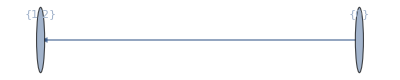

```mathematica
LadderGraph@@{singulars,parentage}
```